```mathematica
KGD  LHFM model
```

Plane-strain linear hydraulic fracture solution
Newtonian Fluid
Constant rate

REFERENCEs:
J. I. Adachi and E. Detournay. Self-similar solution of a plane-strain fracture driven by a power-law fluid. International Journal for Numerical and Analytical Methods in Geomechanics, 26(6):579–604, 2002.

 E. Detournay. Propagation regimes of fluid-driven fractures in impermeable rocks. International Journal of Geomechanics, 4(1):35–45, 2004.
 
  M. Azad, D. Garagash, and M. Satish. Nucleation of dynamic slip on a hydraulically fractured fault. Journal of Geophysical Research: Solid Earth, 122(4):2812–2830, 2017.
(for the stress ahead for the M-vertex solution (zero toughness case) )

```mathematica
MyPathTo = "/Users/bricelecampion/Documents/Work/Geomechanics/HydraulicFracturing/Solutions/RefFDFractures/src/wolfram/"
```

/Users/bricelecampion/Documents/Work/Geomechanics/HydraulicFracturing/Solutions/RefFDFractures/src/wolfram/

```mathematica
Import[MyPathTo<>"ProtectedDefinitions.m"]
Import[MyPathTo<>"KGDSolutions.m"]
```

The solutions are in the package KGDSolutions.

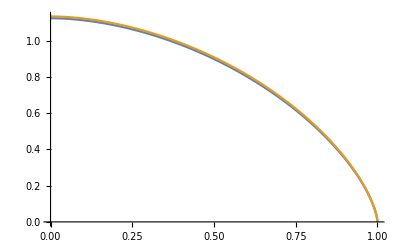

```mathematica
Plot[{Opening/.ZeroToughnessSolution[x],Opening/.ZeroToughnessSolution3Terms[x]},{x,0,1}]
```

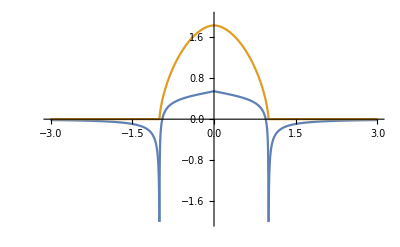

```mathematica
Plot[{NetPressure/.ZeroToughnessSolution[x],Omegabar/.ZeroToughnessSolution[x]},{x,-3,3},PlotRange->{-2,2}]
```

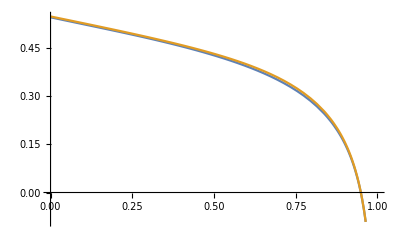

```mathematica
Plot[{NetPressure/.ZeroToughnessSolution[x],NetPressure/.ZeroToughnessSolution3Terms[x]},{x,0,1}]
```

```mathematica
ZeroViscositySolution[x]
```

{gamma→0.932388,NetPressure→0.183074,Omegabar→0.732296 √(1-x^2),Opening→0.682784 √(1-x^2)}

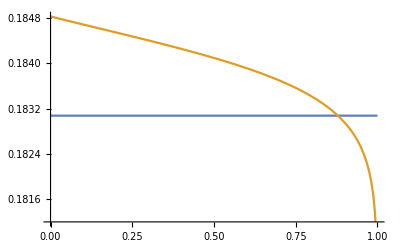

```mathematica
Plot[{NetPressure/.ZeroViscositySolution[x],NetPressure/.SmallViscositySolution[x,0.001]},{x,0,1}]
```

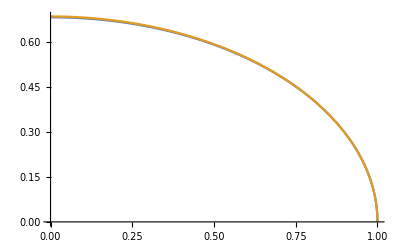

```mathematica
Plot[{Opening/.ZeroViscositySolution[x],Opening/.SmallViscositySolution[x,0.001]},{x,0,1}]
```